-x0^2+x0^4+x1^2

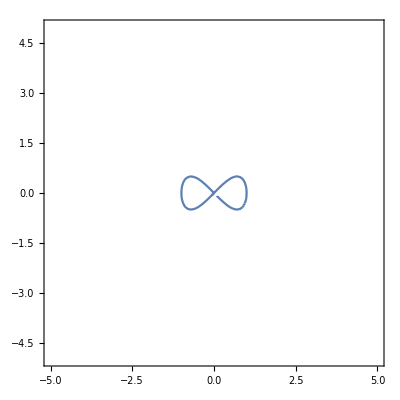

```mathematica
f = x0^4 - x0^2 + x1^2
ContourPlot[f==0,{x0,-5,5},{x1,-5,5}]
```

-u0^4+u0^6-16 u1^2+20 u0^2 u1^2-3 u0^4 u1^2+8 u1^4+3 u0^2 u1^4-u1^6

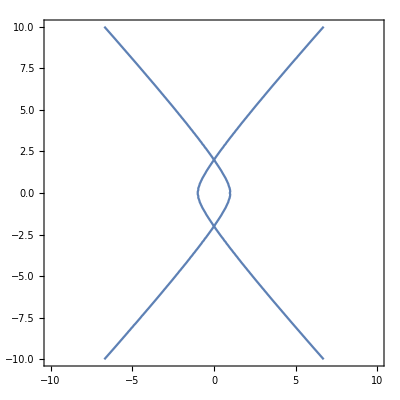

x0^4 - x0^2*x2^2 + x1^2*x2^2

```mathematica
h = ResourceFunction["PolynomialHomogenize"][Expand[f],{x0, x1},x2];
h //InputForm

d = u0^6-3*u0^4*u1^2+3*u0^2*u1^4-u1^6-u0^4*u2^2+20*u0^2*u1^2*u2^2+8*u1^4*u2^2-16*u1^2*u2^4;
s = d /. u2-> 1
ContourPlot[s == 0, {u0, -10, 10}, {u1, -10, 10}]
```